#### Hopping only

```mathematica
H[Nl_]:=Table[If[Abs[i-j]==1,-1,0],{i,1,Nl},{j,1,Nl}];
H[10]//MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

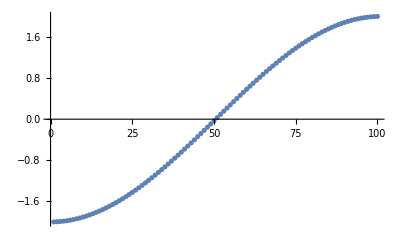

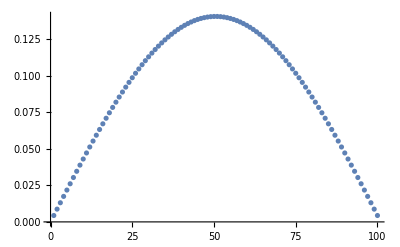
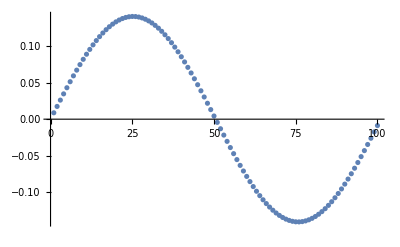
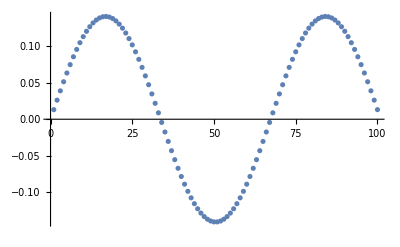
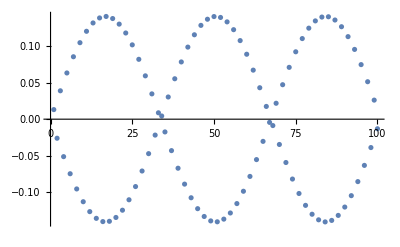
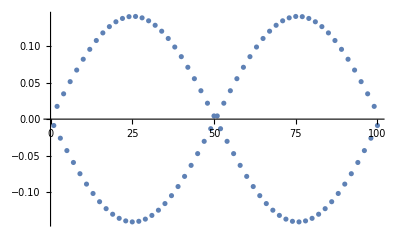
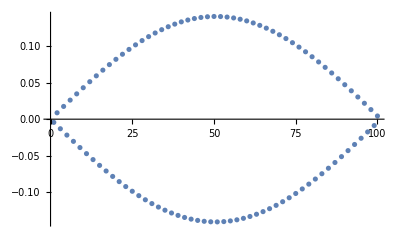

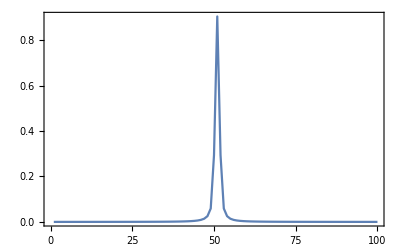

```mathematica
Nl = 100;
{EVals,EVecs}=Eigensystem[N[H[Nl]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]]],ListPlot[sortedEVecs[[2]]],ListPlot[sortedEVecs[[3]]],ListPlot[sortedEVecs[[98]]],ListPlot[sortedEVecs[[99]]], ListPlot[sortedEVecs[[100]]]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```

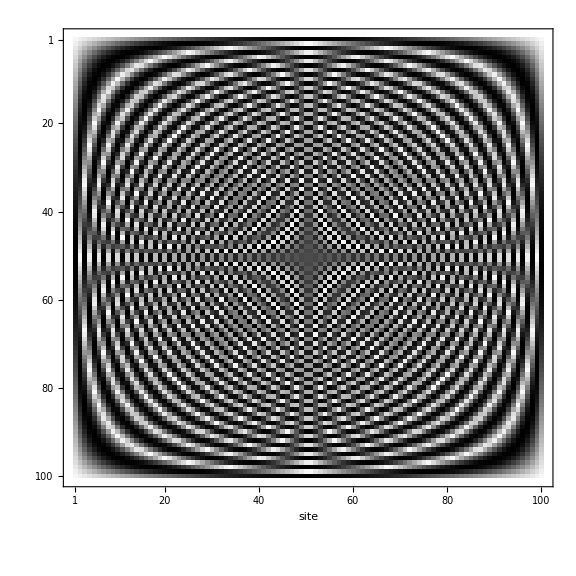

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

```mathematica
ClearAll@ψ;
H[Nl_]:=Table[If[Abs[i-j]==1,-1,0],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 15;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

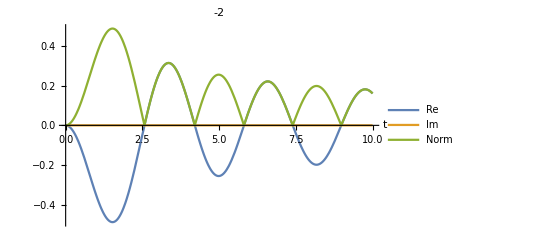
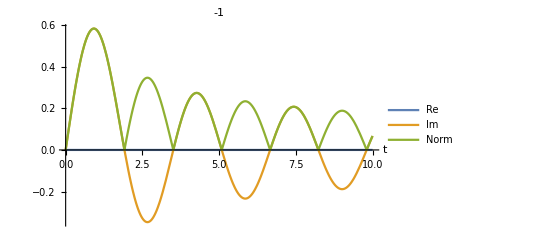
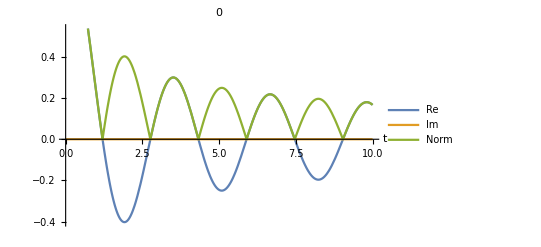
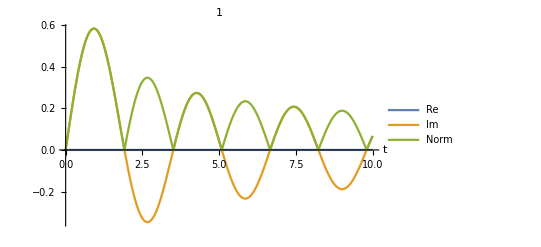
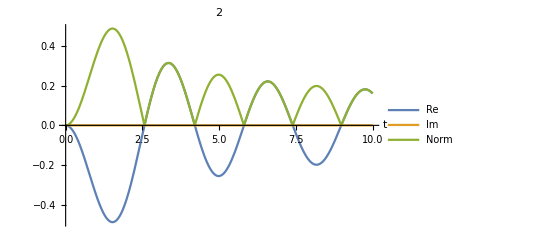

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"}, AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2-2, Nl/2+2}]
(*Manipulate[ListLinePlot[Abs[ψ[t]]^2,PlotRange->{0,1},PlotLabel->t],{t,0,5}]*)
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{t,"site"}, ImageSize->Medium, ColorFunctionScaling->False]
```

#### Calculate hopping

```mathematica
Hij[V0_,q_,i_,j_]:=If[i==j,(2i+q)^2+V0/2,If[Abs[i-j]==1,-1/4 V0,0]];
jMax=3;
H[V0_,q_]:=Table[Hij[V0,q,i,j],{i,-jMax,jMax},{j,-jMax,jMax}]
EV[V_,q_,l_]:=Sort[Transpose[Chop[N[Eigensystem[H[V,q]]]]]] [[l,2]] ;
EVNormed[V_,q_,l_]:=Module[{tmp=EV[V,q,l]},(tmp/Norm[tmp])] ;
Bloch[x_,V_,q_,l_]:=Sum[Exp[π*I (q+2n) x]*EVNormed[V,q,l][[n+jMax+1]],{n,-jMax,jMax}];
```

```mathematica
qqstep=0.1;
PhaseFactor[V_,q_,l_]:=If[OddQ[l],Arg[Bloch[0,V,q,l]],Arg[Bloch[0.25,V,q,l]]];
Wannier[x_,V_,l_,xi_]:=Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,qqstep}]*(qqstep/2)-1/2(Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,2}])*(qqstep/2);
xxstep=0.01;
xlist=Range[-5,5,xxstep];
nWannier=1;
Vlat = 10;
wlist0 = Wannier[xlist,Vlat,nWannier,0];
wlist1 = Wannier[xlist,Vlat,nWannier,1];
```

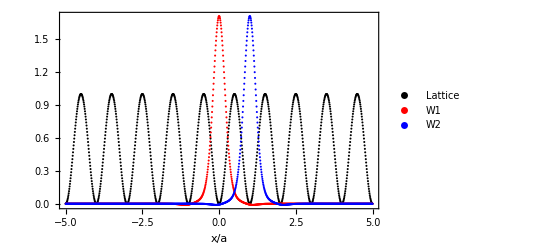

```mathematica
ltslist=Sin[π*xlist]^2;(*lattice potential*)
wlist0Norm=wlist0/√Total[Re[wlist0]^2*xxstep];
wlist1Norm=wlist1/√Total[Re[wlist1]^2*xxstep];ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlist0Norm]}],Transpose[{xlist,Re[wlist1Norm]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","W1","W2"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Blue}}]
```

```mathematica
dw0list=(wlist0[[1;;-3]]+wlist0[[3;;-1]]-2*wlist0[[2;;-2]])/xxstep^2/π^2;(*-ℏ^2/(2m)∂/(∂^2 x) dimensionless version; -ℏ^2/(2m)∂/(∂^2 x)=-(ℏ^2 a^2)/(2m)∂/(∂^2 (x/a))= -(ℏ^2 k0^2)/(2m)∂/(∂^2 (x/a))1/π^2=Er ∂/(∂^2 (x/a))1/π^2*)
Jhop=(Chop[-Total[Re[wlist1[[2;;-2]]]*Re[dw0list]*xxstep]+Total[Vlat*ltslist*Re[wlist0]*Re[wlist1]*xxstep]])(*units of Er*)
```

-0.0191934

### With Trap

Low ω

```mathematica
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
H[10,0.7]//MatrixForm
```

(7.84 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 4.41 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1.96 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0.49 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0. | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0.49 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1.96 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 4.41 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 7.84 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 12.25)

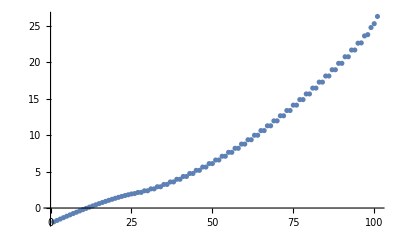

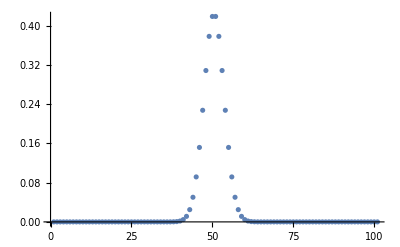
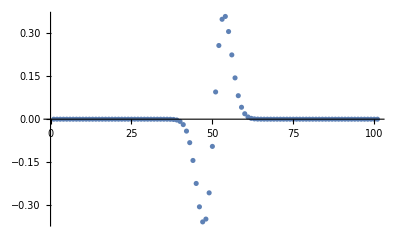
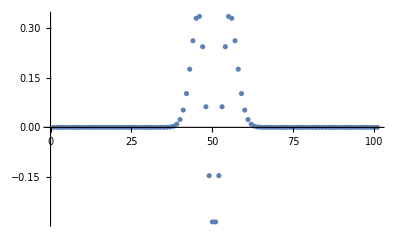
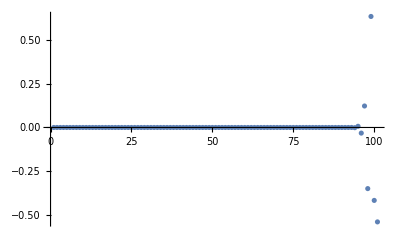
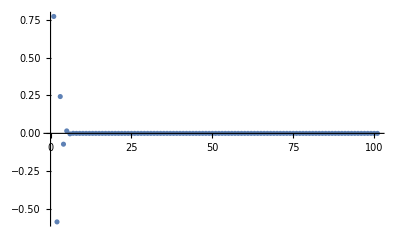

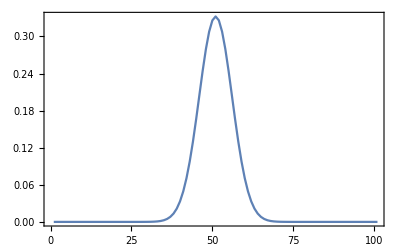
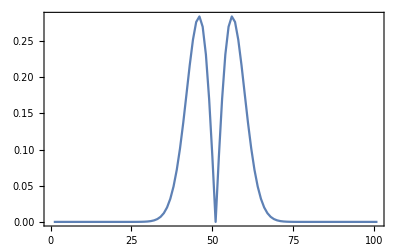

```mathematica
ω = 0.1;
Nl = 101;
{EVals,EVecs}=Eigensystem[N[H[Nl,ω]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large, ColorFunctionScaling->False ]
```

-Graphics-

```mathematica
ClearAll@ψ;
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
ω = 0.1;
Nl = 200;
tf = 70;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, ω] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

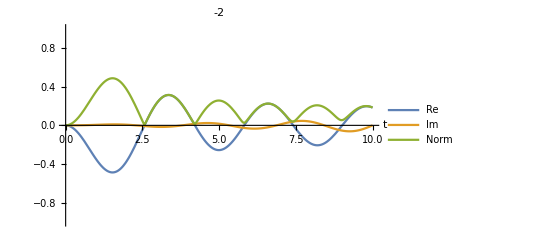
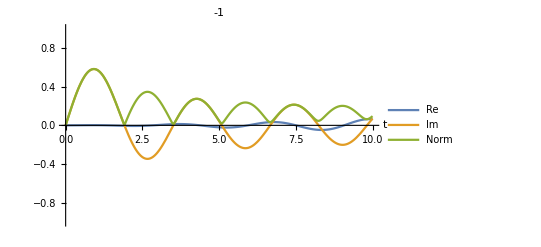
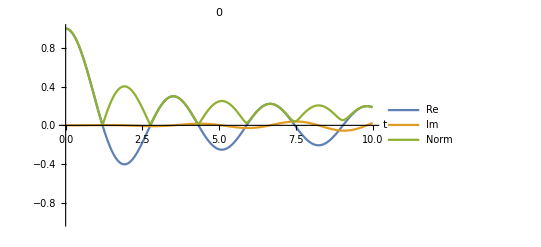
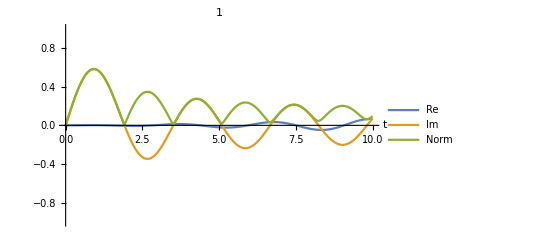
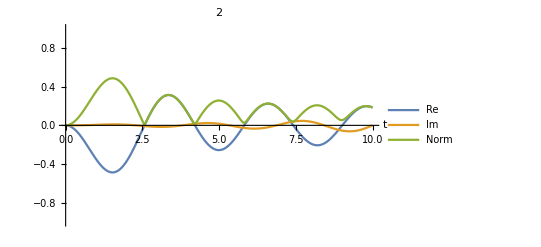

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i-Nl/2], {i, Nl/2-2, Nl/2+2}]
```

```mathematica
sitenum = 198;
tmax = 70;
MatrixPlot[Table[Abs[ψ[t][[1, i]]],  {i, Nl/2-sitenum/2, Nl/2+sitenum/2}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"},  ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

High ω

```mathematica
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
ω = 0.5;
Nl = 100;
{EVals,EVecs}=Eigensystem[N[H[Nl,ω]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];

(*ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}*)
```

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large, ColorFunctionScaling->False ]
```

-Graphics-

```mathematica
ClearAll@ψ;
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
ω = 0.4;
Nl = 100;
tf = 40;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, ω] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

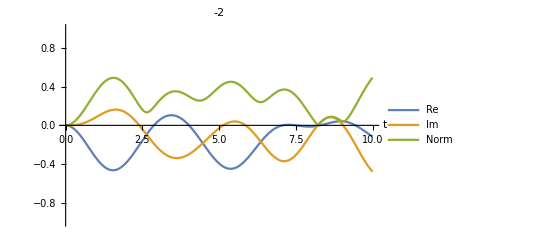
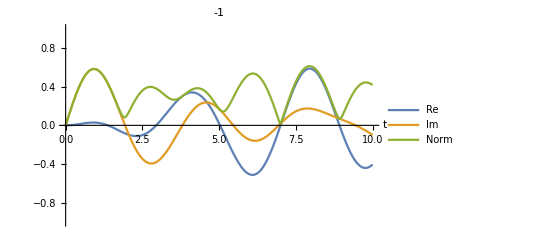
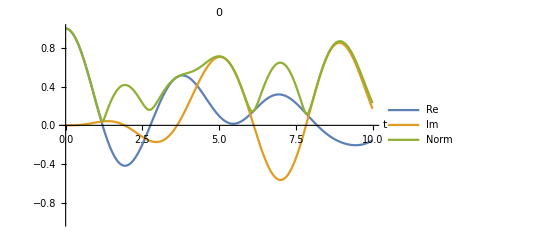
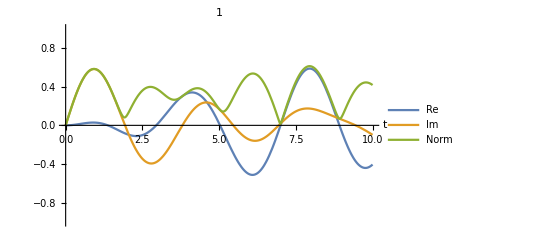
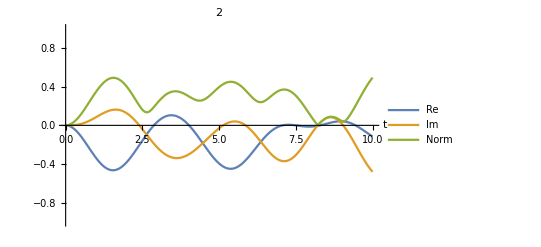

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i-Nl/2], {i, Nl/2-2, Nl/2+2}]
```

```mathematica
sitenum = 48;
tmax = 40;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {i, Nl/2-sitenum/2, Nl/2+sitenum/2}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"},  ImageSize->Full, ColorFunctionScaling->False]
```

-Graphics-

## With force term

```mathematica
H[Nl_, F_]:=Table[If[i==j,F*i,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
H[10,0.5]//MatrixForm
```

(0.5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1.5 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2. | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2.5 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 3. | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 3.5 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 4. | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 4.5 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 5.)

#### Small force

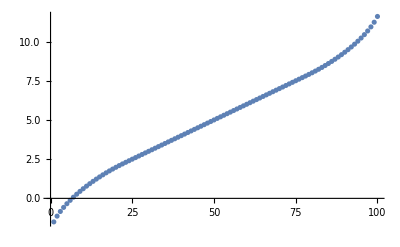

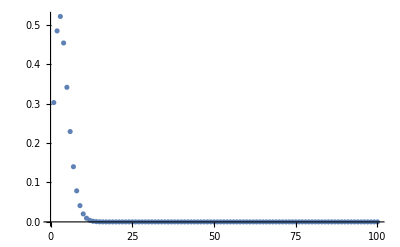
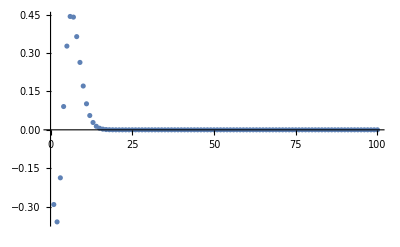
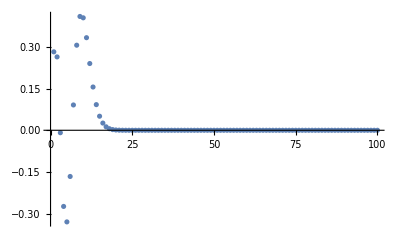
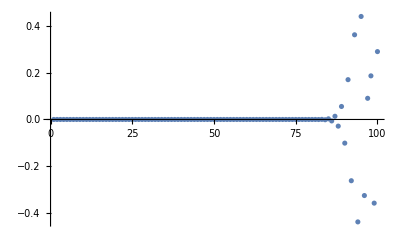
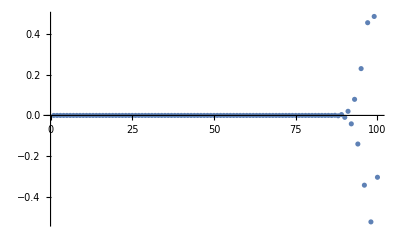

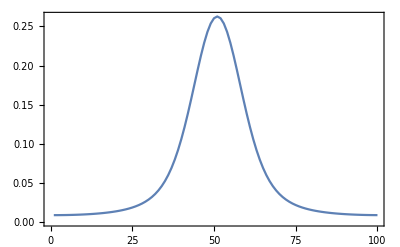
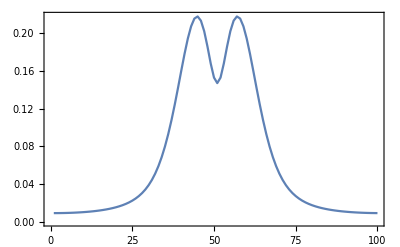

```mathematica
Nl = 100;
F = 0.1;
{EVals,EVecs}=Eigensystem[N[H[100, F]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

```mathematica
ClearAll@ψ;
H[Nl_, F_]:=Table[If[i==j,F*i,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 50;
F = 0.1;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, F] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

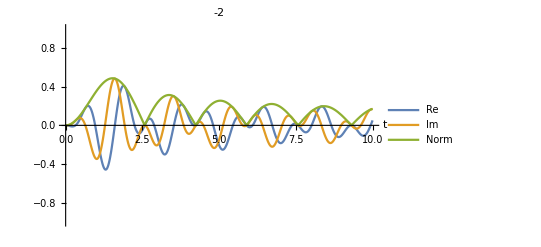
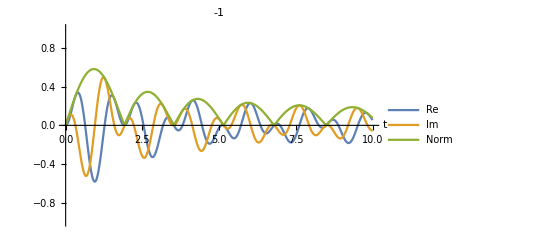
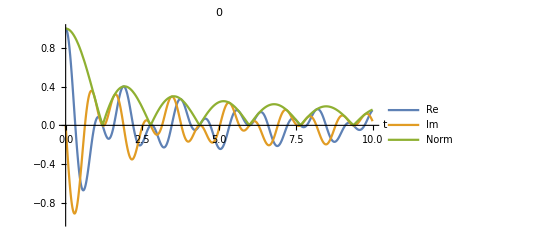
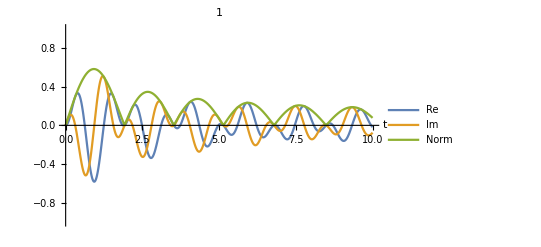
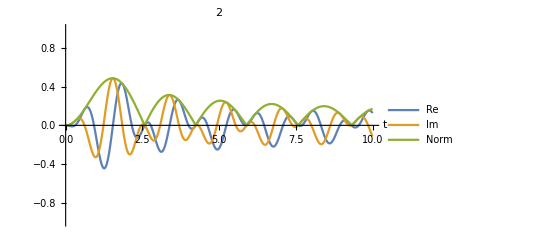

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"}, PlotRange ->{-1, 1},AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 2, Nl/2+2}]
```

```mathematica
(*λ[t_]:= MatrixExp[I H[Nl] t].ψ0;
Table[Plot[{Re[λ[t][[ i]]], Im[λ[t][[ i]]], Norm[λ[t][[i]]]}, {t, 0, tf}, PlotLegends->{"Re","Im","Norm"}, AxesLabel->{"t", ""}, PlotLabel->i], {i, 1, Nl}]*)
```

```mathematica
sitenum = 98;
tmax = 50;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {i, Nl/2-sitenum/2, Nl/2+sitenum/2}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"}, ImageSize->Full, ColorFunctionScaling->False]
```

-Graphics-

#### Larger force

```mathematica
Nl = 100;
F = 0.5;
{EVals,EVecs}=Eigensystem[N[H[100, F]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
(*ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}*)
```

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

```mathematica
ClearAll@ψ;
H[Nl_, F_]:=Table[If[i==j,F*i,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 50;
F = 0.5;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, F] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

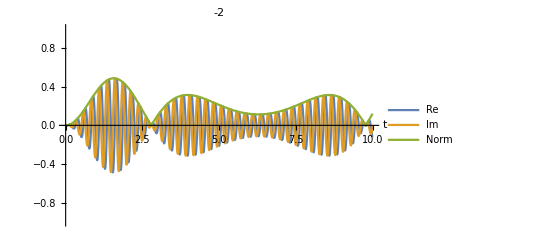
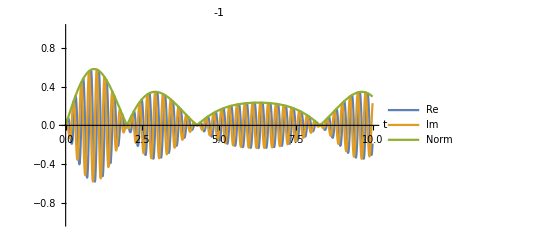
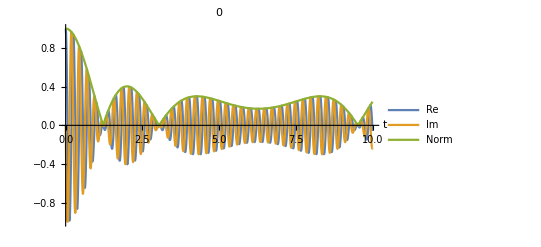
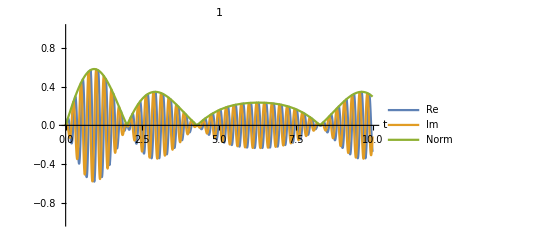
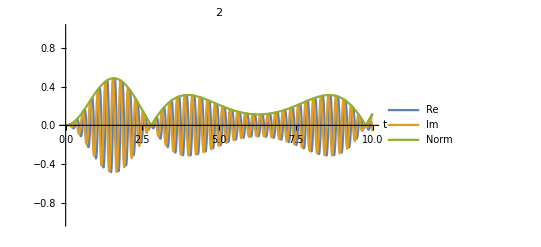

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"}, PlotRange ->{-1, 1},AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 2, Nl/2+2}]
```

```mathematica
sitenum = 48;
tmax = 40;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {i, Nl/2-sitenum/2, Nl/2+sitenum/2}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"}, ImageSize->Full, ColorFunctionScaling->False]
```

-Graphics-

## Time dependent force term - NDSolve

```mathematica
Ht[Nl_,F_, ω_, t_]:=Table[If[i==j, F*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Ht[5,0.5, 0.5, t]//MatrixForm
```

(0.5 Cos[0.5 t] | -1 | 0 | 0 | 0
-1 | 1. Cos[0.5 t] | -1 | 0 | 0
0 | -1 | 1.5 Cos[0.5 t] | -1 | 0
0 | 0 | -1 | 2. Cos[0.5 t] | -1
0 | 0 | 0 | -1 | 2.5 Cos[0.5 t])

#### breathing motion

```mathematica
ClearAll@ψ;
Ht[Nl_,F_, ω_, t_]:=Table[If[i==j, F*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 120;
tf = 300;
F = 1;
ω= 1/N[BesselYZero[0,51]];
F0 = F/ω;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl, F, ω, t] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

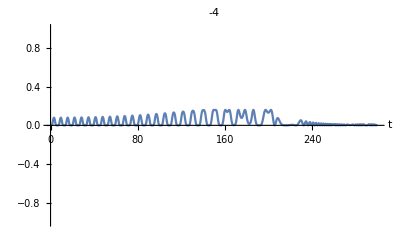
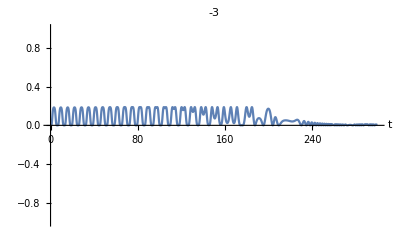
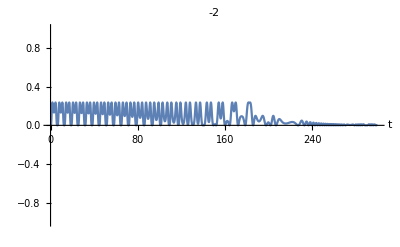
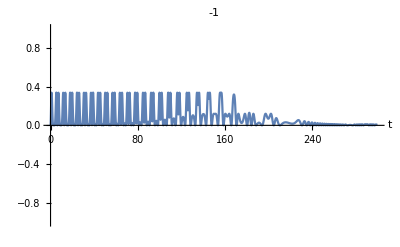
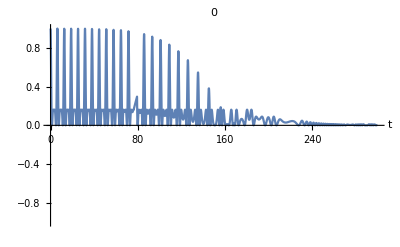
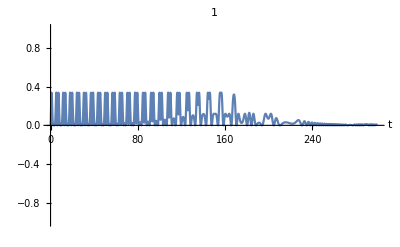
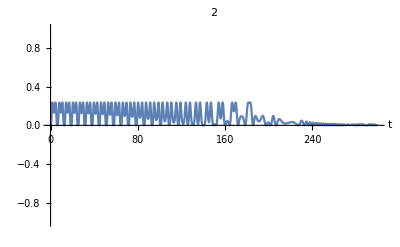
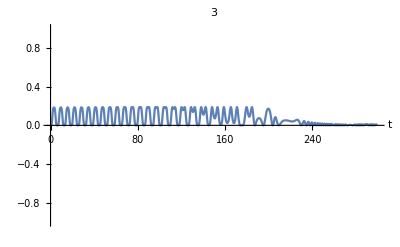

```mathematica
tmax =tf;
(*Table[Plot[ Norm[ψ[t][[1, i]]]*Norm[ψ[t][[1, i]]], {t, 0, tmax},PlotRange ->{-1, 1},  AxesLabel->{"t", ""},  Ticks -> {{0, 2Pi, 4Pi, 6Pi, 8Pi}, {-1, 1}}, PlotLabel->i - Nl/2], {i, Nl/2 - 4, Nl/2 + 4}]*)
Table[Plot[ Norm[ψ[t][[1, i]]]*Norm[ψ[t][[1, i]]], {t, 0, tmax},PlotRange ->{-1, 1},  AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 4, Nl/2 + 4}]
```

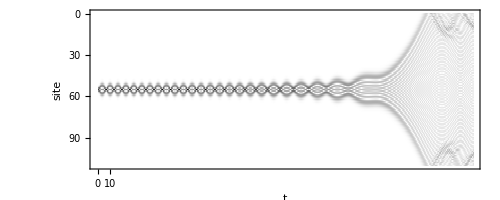

```mathematica
sitenum = 110;
tmax = 300;
xrow=Table[If[Divisible[i, 100]==True,i/10,""],{i,0,tmax*10}];
ycolumn=Table[ If[Divisible[i, 10]==True,i,""],{i,0,sitenum}];
xticks=MapIndexed[{#2[[1]],#}&,xrow];
yticks=MapIndexed[{#2[[1]],#}&,ycolumn];
MatrixPlot[Table[Abs[ψ[t][[1, i]]],  {i, Nl/2-sitenum/2, Nl/2+sitenum/2}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"}, FrameTicks->{{yticks,yticks},{xticks,xticks}}, ImageSize->Full, ColorFunctionScaling->False]
```

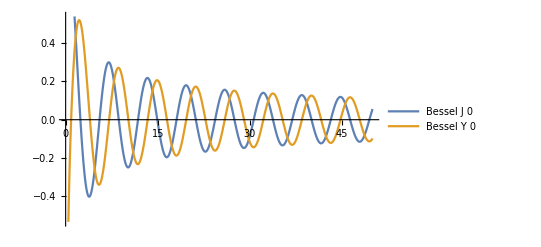

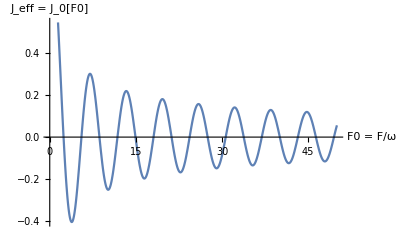

```mathematica
N[BesselYZero[0,3]];
Plot[{BesselJ[0,x],BesselY[0, x]}, {x, 0, 50},  PlotLegends->{"Bessel J 0","Bessel Y 0"}]
Plot[{BesselJ[0,x]}, {x, 0, 50},  AxesLabel->{"F0 = F/ω", "J_eff = J_0[F0]"}]
```

## Gaussian potential

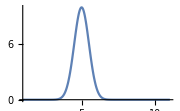

```mathematica
Gaus[a_, b_, c_, x_, midx_, ω_, t_]:= N[Chop[a*Exp[Chop[(-(x-midx- b*Sin[ω*t])^2)/(2*c^2)]]]];
Plot[Gaus[10, 3, 0.5,  5,x, 1, 0], {x, 1, 11}, PlotRange->Full, ImageSize-> Small]
```

```mathematica
Ht[Nl_,a_, b_, c_,  ω_, t_]:=Table[If[i==j, Gaus[a, b, c, Ceiling[Nl/2], i, ω, t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Ht[7,1, 1, 0.5, 1, 0]//MatrixForm
```

(1.523×10^-8 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0.000335463 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0.135335 | -1 | 0 | 0 | 0
0 | 0 | -1 | 1. | -1 | 0 | 0
0 | 0 | 0 | -1 | 0.135335 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0.000335463 | -1
0 | 0 | 0 | 0 | 0 | -1 | 1.523×10^-8)

```mathematica
ClearAll@ψ;
tf = 20;
Nl = 101;
midx = Ceiling[Nl/2];
a = 10;
b = 3;
c = 0.5;
ω = 1;
ψ0 = Table[If[i==midx,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl,a, b, c, ω, t].ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

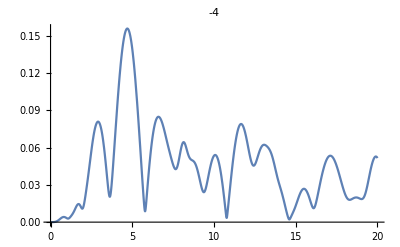
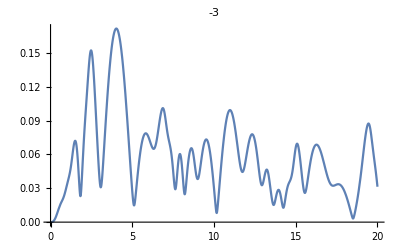
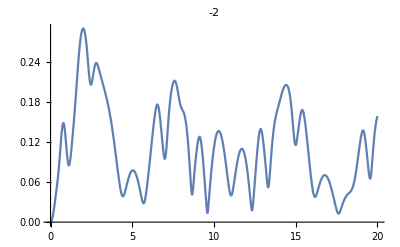
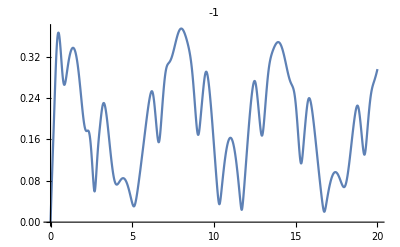
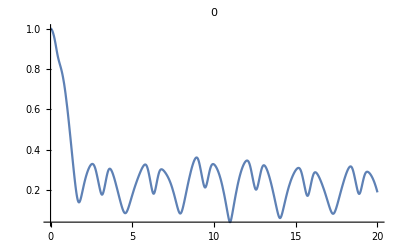
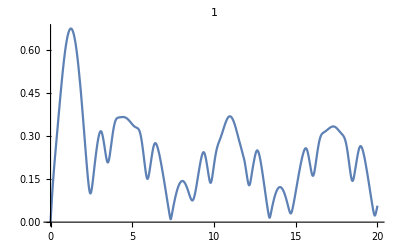
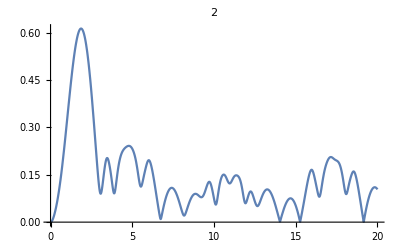
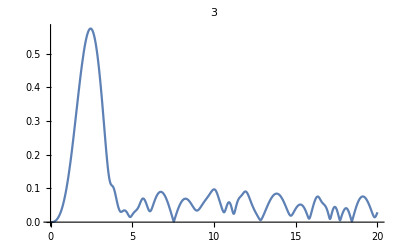

```mathematica
Table[Plot[Norm[ ψ[t][[1, i]]], {t, 0, tf},PlotRange ->Full, PlotLabel -> i - midx], {i, midx - 4, midx+4}]
```

```mathematica
siteside = Floor[Nl/2]
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {i, midx-siteside, midx+siteside}, {t, 0, tf, 0.1}], FrameLabel->{"site","t"}, ImageSize->Full, ColorFunctionScaling->False]
```

50

-Graphics-